# Problema 6

Definimos constantes

```mathematica
Clear["Global`*"]
G=1;
M1 = 10.0;
M2 = 20.0;
m = 0.25;
r21 = 1;
u1 = M2/(M1+M2);
u2 = -M1/(M1+M2);
xlim = 1;
ylim = 1;
```

Potencial efectivo en función de “x” y “y”:

```mathematica
Ueff[u_,v_] =((G*(M1+M2)*m)/r21)*((u2/Sqrt[(u-u1)^2+v^2])  -(u1/Sqrt[(u-u2)^2+v^2]) -(1/2)*(u^2+v^2));
```

## Parte b)

Gráfico del Potencial Efectivo(Ueff) vs Posición(x,y) de la masa “m”:

```mathematica
Plot3D[Ueff[u,v],{u,-xlim-0.5,xlim+0.5},{v,-ylim-0.5, ylim+0.5}, 
											ImageSize->Large, 
											AxesLabel->{"u","v","Ueff(u,v)"},
											BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

-Graphics3D-

## Parte c)

```mathematica
DerivadaPotencialu[u_,v_] = FullSimplify[D[Ueff[u,v],u]];
DerivadaPotencialv[u_,v_] = FullSimplify[D[Ueff[u,v],v]];
```

```mathematica
Solve[{DerivadaPotencialu[u,v]==0, DerivadaPotencialv[u,v] == 0},{u,v}]
```

{{u→0.166667,v→-0.866025},{u→-1.13636,v→0.},{u→0.237418,v→0.},{u→1.24905,v→0.},{u→0.166667,v→0.866025}}

Guardo las posiciones de los puntos de Lagrange para luego graficarlos

```mathematica
PuntosLagrange = {{0.167,-0.866 }, {-1.136,0},{0.237,0},{1.249,0},{0.167,0.866 }};
```

## Parte d)

Defino el set de valores de las curvas equipotenciales:

```mathematica
SetofContours = #&/@Range[-16,-10.5,0.5];
```

Gráfico de curvas equipotenciales:

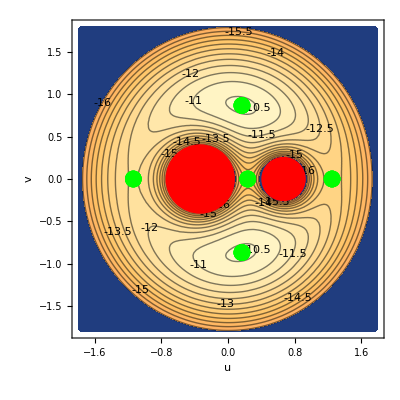

```mathematica
ContourPlot[Ueff[u,v],{u,-1.8,1.8},{v,-1.8,1.8}, Contours->SetofContours, ContourLabels->(Text[Framed[#3],{#1,#2},Background->LightBlue]&),
													ImageSize->Full, FrameLabel->{"u","v"},
													BaseStyle->{FontWeight->"Bold",FontSize->18},
			Epilog->{  {PointSize[0.03], Green, Point[#] & /@ PuntosLagrange, Text["L1", PuntosLagrange[[2]],{0,3}] },
					{PointSize[0.03], Green, Point[#] & /@ PuntosLagrange, Text["L2", PuntosLagrange[[3]],{0,-3}] },
					{PointSize[0.03], Green, Point[#] & /@ PuntosLagrange, Text["L3", PuntosLagrange[[4]],{0,3}] },
					{PointSize[0.03], Green, Point[#] & /@ PuntosLagrange, Text["L4", PuntosLagrange[[1]],{2,2}] },
					{PointSize[0.03], Green, Point[#] & /@ PuntosLagrange, Text["L5", PuntosLagrange[[5]], {2,-2}] },
					{PointSize[0.08], Red,Point[{{u1,0}}], Text["M1",{u1,0}, {4,4}]},
					{PointSize[0.13], Red,Point[{{u2,0}}],  Text["M2",{u2,0}, {5,5}]} }]
```

```mathematica
PuntosLagrange[[1]]
```

{0.167,-0.866}